# Codificación Huffman

La codificación Huffman representa un conjunto de símbolos en otra representación de más baja entropía mediante la constucción de un árbol binario donde cada nodo son los símbolos del alfabeto. La construcción de este árbol binario se realiza conectando los nodos de menor probabilidad de aparición. De esta manera se obtiene una representación de menor entropía para los nodos más frecuentes.
-Graphics-

```mathematica
(* Función Encode de: http://rosettacode.org/wiki/Huffman_coding *)
HuffmanEncode[s_String]:=HuffmanEncode[Characters[s]];
HuffmanEncode[l_List]:=Module[{merge,structure,rules},(*merge front two branches.list is assumed to be sorted*)merge[k_]:=Replace[k,{{a_,aC_},{b_,bC_},rest___}:>{{{a,b},aC+bC},rest}];
structure=FixedPoint[Composition[merge,SortBy[#,Last]&],Tally[l]][[1,1]];
rules=(#->Flatten[Position[structure,#]-1])&/@DeleteDuplicates[l];
{Flatten[l/.rules],rules}];

HuffmanDecode[decodestring_,rules_]:= Module[{invrules, decoded,i,rep},
invrules = Map[Reverse,rules];
decoded = {};
i= 1;
While[i≤ Length[decodestring],
Do[
rep = Replace[decodestring[[i;;j]] , invrules];
If[Length[rep] == 0,
AppendTo[decoded, rep];
i = j+1;
Break[];
];
,{j,i+1,Length[decodestring]}
]
];
Return[decoded];
];

HuffmanCompress[l_] := Module[{string, dict, dictsize,padding, compressed,h,ToDigit,ToBinary},
ToDigit[list_] := {Length[list],FromDigits[list,2]};
ToBinary[nlist_]:= FromDigits[nlist,2];
h = HuffmanEncode[l];
string = Map[ToBinary,Partition[h[[1]],8,8,1,0]];
padding = {Mod[Length[h[[1]]],8]};
dict = Flatten[Transpose[{h[[2]][[All,1]],Map[ToDigit,h[[2]][[All,2]]]}],2];
dictsize = {Length[dict]};
compressed = Join[dictsize,padding,dict,string];
Return[compressed];
];

HuffmanDecompress[string_] := Module[{dictsize,padding, dict, code, codeentries,codezerotable,ZeroArray,dictSmallTable,dictzerotable,dictEntries,dictionary},
ZeroArray[size_]:=ConstantArray[0,size];
dictsize = string[[1]];
padding = string[[2]];
dict = Partition[string[[3;;dictsize+2]],3];
codeentries =IntegerDigits[string[[dictsize+3;;-1]],2];
codezerotable =Map[ZeroArray,8-Map[Length,codeentries]];
code =  Table[Flatten[Prepend[codeentries[[i]],codezerotable[[i]]]],{i,1,Length[codeentries]}];
code =Flatten[code][[1;;-1-padding]];
dictSmallTable= IntegerDigits[dict[[All,3]],2];
dictzerotable =Map[ZeroArray,dict[[All,2]]-Map[Length,dictSmallTable]];
dictEntries = Table[Flatten[Prepend[dictSmallTable[[i]],dictzerotable[[i]]]],{i,1,Length[dictSmallTable]}];
dictionary = Table[dict[[All,1]][[i]] -> dictEntries[[i]],{i,1,Length[dict]}];
Return[HuffmanDecode[code,dictionary]];
];

MakeTree[s_String]:= MakeTree[Characters[s]];
MakeTree[l_List] := Module[{merge,structure,tree},
merge[k_]:=Replace[k,{{a_,aC_},{b_,bC_},rest___}:>{{{a,b},aC+bC},rest}];
structure=FixedPoint[Composition[merge,SortBy[#,Last]&],Tally[l]][[1,1]];
tree = {};
AddNode[s_]:=(
If[Length[s] == 2,
If[Length[s[[1]]] == 2,
AppendTo[tree, s-> s[[1]]];
AddNode[s[[1]]];,

AppendTo[tree, {s-> s[[1]],s[[1]]}];
];

If[Length[s[[2]]] == 2,
AppendTo[tree, s-> s[[2]]];
AddNode[s[[2]]];,

AppendTo[tree, {s-> s[[2]],s[[2]]}];
];
];
);
AddNode[structure];
Print[TreePlot[tree]];
];
```

## Compresión de texto

Uno de los ejemplos más triviales para demostrar la codificación huffman es la compresión de texto. En esta implementación la compresión se hace por medio de un diccionario. Se puede obtener el resultado del texto comprimido y las reglas del diccionario de la siguiente manera.

```mathematica
texto ="En el principio creó Dios los cielos y la tierra. Y la tierra estaba desordenada y vacía, y las tinieblas estaban sobre la faz del abismo, y el Espíritu de Dios se movía sobre la faz de las aguas. Y dijo Dios: Sea la luz; y fue la luz. Y vio Dios que la luz era buena; y separó Dios la luz de las tinieblas. Y llamó Dios a la luz Día, y a las tinieblas llamó Noche. Y fue la tarde y la mañana un día.";
HuffmanEncode[texto]
```

{{1,1,1,0,1,0,1,1,0,1,0,0,1,0,0,1,1,0,0,1,1,0,1,0,0,1,1,1,0,1,0,0,1,0,1,1,0,0,1,1,0,0,1,0,0,1,0,1,0,1,0,0,0,1,1,0,1,1,1,0,1,0,0,0,1,1,0,1,1,1,1,0,0,0,0,1,0,1,0,0,1,0,1,1,0,1,1,0,0,1,1,1,0,0,1,1,0,0,1,0,1,1,1,0,0,1,1,0,1,1,1,1,0,1,0,1,0,0,0,1,1,0,1,1,1,1,1,0,1,0,1,0,0,0,0,1,0,1,0,0,0,1,1,0,1,1,0,0,1,1,0,1,1,1,1,1,0,1,0,1,0,0,0,1,1,1,0,0,0,0,0,1,1,0,1,1,0,0,0,0,1,1,1,1,1,1,0,1,1,0,1,1,0,0,1,0,1,1,0,1,0,1,1,0,1,0,0,0,1,1,1,1,0,0,0,0,1,0,1,1,1,0,0,1,1,0,1,1,0,0,0,0,1,1,1,1,1,1,0,1,1,0,1,1,0,0,1,0,1,1,0,1,0,1,1,0,1,0,0,0,0,1,1,0,0,1,0,1,0,1,1,1,1,1,1,1,0,0,1,1,1,1,1,0,1,0,0,0,0,0,1,0,0,0,1,1,0,0,1,0,1,0,1,1,1,1,0,1,0,1,1,0,0,1,0,0,0,1,1,0,0,0,1,0,0,1,1,0,0,0,1,0,0,0,1,0,0,0,0,1,1,1,0,0,0,0,0,0,1,1,1,1,1,1,1,0,0,0,1,0,1,0,0,0,1,0,1,0,1,1,0,0,0,1,1,1,1,1,0,0,0,1,1,1,0,0,0,0,0,1,1,0,1,1,0,0,1,0,1,0,0,0,1,1,1,1,1,1,0,1,1,0,0,1,0,0,1,0,1,1,0,1,1,0,0,1,1,1,1,1,0,1,1,0,1,1,0,0,1,0,1,0,0,0,1,1,0,0,1,0,1,0,1,1,1,1,1,1,1,0,0,1,1,1,1,1,0,1,0,0,0,1,0,0,1,0,0,1,0,1,0,1,1,1,1,0,1,1,1,1,1,0,1,0,1,1,0,1,1,0,0,0,0,1,1,0,1,1,0,0,0,0,1,1,1,0,0,1,0,1,0,0,1,0,1,1,1,1,0,0,0,1,0,0,0,1,1,0,0,1,1,0,1,0,0,1,0,0,1,1,1,1,1,0,0,1,1,0,1,0,1,0,0,1,0,1,1,0,1,1,1,1,0,0,1,1,1,1,1,0,0,0,1,1,1,0,0,0,0,0,1,1,0,0,1,1,0,1,0,0,1,1,1,0,1,0,1,1,1,0,1,0,1,1,1,0,1,0,0,0,1,0,1,0,1,1,0,1,1,0,0,1,1,0,1,1,1,1,1,1,0,1,1,1,0,0,0,0,1,0,0,0,1,1,0,0,0,0,1,0,1,1,1,0,0,1,1,0,1,1,1,1,0,1,0,1,0,0,0,1,0,1,0,1,1,0,0,0,0,0,1,0,1,1,0,1,1,1,1,0,0,1,1,1,1,1,1,0,1,0,1,0,1,1,0,0,0,0,1,0,1,0,1,1,1,1,0,1,1,1,1,1,0,1,0,1,1,0,1,1,0,0,0,0,1,1,0,1,1,0,0,0,0,1,1,1,0,0,1,0,1,0,0,1,0,1,1,1,1,0,0,0,1,0,0,0,1,1,0,0,0,0,1,1,0,1,1,0,0,1,0,1,0,0,0,1,0,0,1,1,1,0,1,1,0,0,1,0,1,1,1,0,1,0,0,1,0,1,0,0,1,1,1,1,0,0,0,0,1,0,1,1,1,0,0,0,1,0,0,0,0,1,1,0,1,1,1,0,1,1,0,1,1,1,1,1,1,0,0,0,1,0,1,1,1,0,0,1,1,0,1,1,1,1,0,1,0,1,0,1,1,1,0,1,1,0,0,0,0,0,1,1,1,0,1,1,1,1,1,1,1,0,0,1,0,0,0,0,1,1,0,1,1,0,0,0,0,1,1,0,1,0,1,1,1,0,1,0,1,1,1,1,1,1,1,0,1,0,1,0,0,0,1,1,1,0,0,0,0,0,1,1,1,0,0,1,0,0,1,1,1,0,1,1,0,0,0,0,1,1,0,1,1,0,0,0,0,1,1,0,1,0,1,1,1,0,1,0,1,1,1,1,0,1,1,1,1,0,0,0,0,1,0,1,1,1,0,0,0,1,1,1,1,1,1,0,1,1,0,1,1,1,1,0,0,0,1,0,1,1,1,0,0,1,1,0,1,1,1,1,0,1,0,1,0,0,0,1,1,1,0,1,1,1,1,0,0,1,1,1,0,1,1,0,0,0,0,1,1,0,1,1,0,0,0,0,1,1,0,1,0,1,1,1,0,1,0,1,1,1,1,0,0,1,1,0,0,1,0,1,1,0,1,0,0,0,0,1,1,1,1,1,0,0,1,1,1,0,1,1,0,0,0,1,0,0,1,1,0,0,1,1,1,0,1,0,1,0,0,0,1,1,1,0,0,0,0,0,1,0,1,0,1,1,0,0,1,1,1,0,1,0,0,1,0,0,1,0,1,1,0,1,1,1,0,0,1,1,0,0,1,0,1,1,1,0,0,1,1,0,1,1,1,1,0,1,0,1,0,0,0,1,1,0,1,1,0,0,0,0,1,1,0,1,0,1,1,1,0,1,0,1,1,1,1,0,0,0,1,0,0,0,1,1,0,0,0,0,1,1,0,1,1,0,0,1,0,1,0,0,0,1,1,1,1,1,1,0,1,1,0,0,1,0,0,1,0,1,1,0,1,1,0,0,1,1,1,1,1,0,1,1,0,1,1,0,0,1,0,1,0,0,1,1,1,1,0,0,0,0,1,0,1,1,1,0,0,1,1,0,1,1,1,0,1,1,0,0,0,1,0,1,1,0,1,1,1,0,0,1,1,0,0,1,0,1,1,1,0,0,1,1,0,1,1,1,1,0,1,0,1,0,0,0,1,0,0,0,0,1,1,0,1,1,0,0,0,0,1,1,0,1,0,1,1,1,0,1,0,1,1,1,1,0,0,1,0,1,1,1,0,0,1,0,1,0,1,1,0,0,0,1,1,1,1,1,0,0,0,1,1,1,0,0,0,0,0,1,0,0,0,0,1,1,0,1,1,0,0,1,0,1,0,0,0,1,1,1,1,1,1,0,1,1,0,0,1,0,0,1,0,1,1,0,1,1,0,0,1,1,1,1,1,0,1,1,0,1,1,0,0,1,0,1,0,0,0,1,1,0,1,1,1,0,1,1,0,0,0,1,0,1,1,0,1,1,1,0,0,1,1,0,0,1,1,1,0,1,1,1,0,1,1,1,1,1,0,0,1,0,1,0,0,1,1,1,0,1,1,0,1,0,1,1,0,0,0,1,1,1,1,0,0,0,0,1,0,1,1,1,0,0,1,1,1,0,0,1,0,0,1,1,1,0,1,1,0,0,0,0,1,1,0,1,1,0,0,0,0,1,1,1,1,1,1,1,0,0,1,0,1,1,0,0,1,0,0,0,1,1,0,0,0,0,1,1,1,0,0,0,0,0,1,1,0,1,1,0,0,0,0,0,1,0,1,1,0,1,0,0,1,1,1,0,1,1,1,0,0,1,0,0,0,1,0,0,1,1,0,0,0,0,0,1,1,1,0,0,1,0,0,1,0,0,0,1,0,0,0,0,1,0,1,0,1,1,0,0,0,1,1,1,1,0},{E→{1,1,1,0,1,0,1,1},n→{0,1,0,0,1}, →{0,0},e→{1,1,0,0},l→{1,1,0,1},p→{1,1,1,0,1,0,0},r→{1,0,1,1,0},i→{0,1,1,0},c→{0,1,0,1,0,0},o→{1,1,1,1,0},ó→{1,1,1,0,0,1,1},D→{1,0,1,1,1,0},s→{1,0,1,0},y→{1,1,1,0,0,0},a→{1,0,0},t→{1,1,1,1,1,1},.→{0,1,1,1,1,0},Y→{0,1,0,1,1,1},b→{1,1,1,1,1,0},d→{0,1,0,0,0},v→{0,1,1,1,1,1,1},í→{0,1,0,1,0,1},,→{0,1,1,1,1,1,0},f→{1,1,1,0,0,1,0},z→{1,0,1,1,1,1},m→{0,1,0,1,1,0},u→{0,1,1,1,0},g→{1,1,1,0,1,1,0,0,1},j→{1,1,1,0,1,1,0,1,1},:→{1,1,1,0,1,1,0,0,0},S→{1,1,1,0,1,1,1,1,1},;→{1,1,1,0,1,0,1,0},q→{1,1,1,0,1,1,1,1,0},N→{1,1,1,0,1,1,1,0,1},h→{1,1,1,0,1,1,0,1,0},ñ→{1,1,1,0,1,1,1,0,0}}}

Para hacer compacta esta representación se convierten los números de binario a decimal. En las dos primeras entradas se guarda la longitud del diccionario y el número de bytes de padding de la cadena codificada.

```mathematica
texto ="En el principio creó Dios los cielos y la tierra. Y la tierra estaba desordenada y vacía, y las tinieblas estaban sobre la faz del abismo, y el Espíritu de Dios se movía sobre la faz de las aguas. Y dijo Dios: Sea la luz; y fue la luz. Y vio Dios que la luz era buena; y separó Dios la luz de las tinieblas. Y llamó Dios a la luz Día, y a las tinieblas llamó Noche. Y fue la tarde y la mañana un día.";
comprimido= HuffmanCompress[texto]
```

{108,4,E,8,235,n,5,9, ,2,0,e,4,12,l,4,13,p,7,116,r,5,22,i,4,6,c,6,20,o,5,30,ó,7,115,D,6,46,s,4,10,y,6,56,a,3,4,t,6,63,.,6,30,Y,6,23,b,6,62,d,5,8,v,7,63,í,6,21,,,7,62,f,7,114,z,6,47,m,6,22,u,5,14,g,9,473,j,9,475,:,9,472,S,9,479,;,8,234,q,9,478,N,9,477,h,9,474,ñ,9,476,235,73,154,116,179,37,70,232,222,20,182,115,46,111,81,190,161,70,205,245,28,27,15,219,45,104,240,185,176,253,178,214,134,87,243,232,35,43,214,70,38,34,28,15,226,138,199,199,6,202,63,100,182,125,178,140,175,231,209,37,123,235,97,176,229,47,17,154,79,154,150,243,227,131,52,235,174,138,217,191,112,140,46,111,81,88,45,231,234,194,189,245,176,216,114,151,136,195,101,19,178,233,79,11,136,110,223,139,155,213,216,59,249,13,134,186,254,163,131,147,176,216,107,175,120,92,126,222,46,111,81,222,118,27,13,117,230,90,31,59,19,58,142,10,206,146,220,203,155,212,108,53,215,136,195,101,31,178,91,62,217,79,11,155,177,110,101,205,234,33,176,215,94,92,172,124,112,67,101,31,178,91,62,217,70,236,91,153,221,242,157,172,120,92,228,236,54,31,203,35,14,13,130,211,185,19,7,36,66,177,224}

El diccionario guarda la estructura del árbol con el que fue creado.

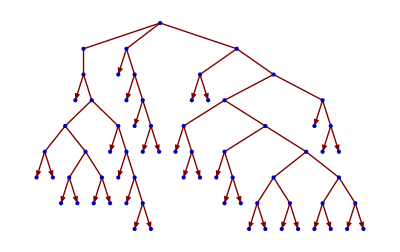

```mathematica
MakeTree[texto];
```

Para este simple ejemplo se alcanza una tasa de compresión de

```mathematica
100*N[Length[comprimido]/Length[Characters[texto]]]
```

80.25

Por último para descomprimir se utiliza el diccionario para reemplazar los elementos.

```mathematica
HuffmanDecompress[comprimido]
```

{E,n, ,e,l, ,p,r,i,n,c,i,p,i,o, ,c,r,e,ó, ,D,i,o,s, ,l,o,s, ,c,i,e,l,o,s, ,y, ,l,a, ,t,i,e,r,r,a,., ,Y, ,l,a, ,t,i,e,r,r,a, ,e,s,t,a,b,a, ,d,e,s,o,r,d,e,n,a,d,a, ,y, ,v,a,c,í,a,,, ,y, ,l,a,s, ,t,i,n,i,e,b,l,a,s, ,e,s,t,a,b,a,n, ,s,o,b,r,e, ,l,a, ,f,a,z, ,d,e,l, ,a,b,i,s,m,o,,, ,y, ,e,l, ,E,s,p,í,r,i,t,u, ,d,e, ,D,i,o,s, ,s,e, ,m,o,v,í,a, ,s,o,b,r,e, ,l,a, ,f,a,z, ,d,e, ,l,a,s, ,a,g,u,a,s,., ,Y, ,d,i,j,o, ,D,i,o,s,:, ,S,e,a, ,l,a, ,l,u,z,;, ,y, ,f,u,e, ,l,a, ,l,u,z,., ,Y, ,v,i,o, ,D,i,o,s, ,q,u,e, ,l,a, ,l,u,z, ,e,r,a, ,b,u,e,n,a,;, ,y, ,s,e,p,a,r,ó, ,D,i,o,s, ,l,a, ,l,u,z, ,d,e, ,l,a,s, ,t,i,n,i,e,b,l,a,s,., ,Y, ,l,l,a,m,ó, ,D,i,o,s, ,a, ,l,a, ,l,u,z, ,D,í,a,,, ,y, ,a, ,l,a,s, ,t,i,n,i,e,b,l,a,s, ,l,l,a,m,ó, ,N,o,c,h,e,., ,Y, ,f,u,e, ,l,a, ,t,a,r,d,e, ,y, ,l,a, ,m,a,ñ,a,n,a, ,u,n, ,d,í,a,.}